## Model Output Generation for Basis Expansion Unit Tests

The hope is that by typing it here in Mathematica with pretty-print, I will duplicate the equations correctly. Then I can use the output from these equations as model outputs for the unit tests that construct the H matrix.

```mathematica
L=10.;
b=1/6.;
a=1.;
V0=100;
nb=10;
```

```mathematica
Fnm[n_,m_,x_]:=If[n==m,x/L-Sin[2 π n x/L]/(2π n),Sin[(m-n)π x/L]/(π(m-n))-Sin[(m+n)π x/L]/(π(m+n))];
```

```mathematica
hnm[n_,m_,s_,b_]:=Fnm[n,m,s+b/2]-Fnm[n,m,s-b/2];
xr[x_,r_]:=-a/2+r a;
```

```mathematica
TFnm[x_]:=Table[{n,m,x,Fnm[n,m,x]},{n,10},{m,10}]//Flatten//Partition[#,4]&;
```

```mathematica
Export["/Users/trunks/codes/782/tests/model/Fnm.08.dat",TFnm[0.8],"Table"]
```

/Users/trunks/codes/782/tests/model/Fnm.08.dat

```mathematica
Thnm[x_,r_]:=Table[{n,m,r, x,hnm[n,m,xr[x,r],b]},{n,10},{m,10}]//Flatten//Partition[#,5]&;
```

```mathematica
xs={0.1,0.3,0.5,0.8};
rs={1,3,5,9};
```

```mathematica
Do[fname=StringForm["/Users/trunks/codes/782/tests/model/hnm.``_``.dat",xi,ri]//ToString;
Export[fname,Thnm[xs⟦xi⟧,rs⟦ri⟧]];,
{xi,Length[xs]},{ri,Length[rs]}]
```

```mathematica
En0[n_]:=n^2 π^2/L^2;
```

```mathematica
Export["/Users/trunks/codes/782/tests/model/En0.dat",Table[En0[n],{n,100}],"Table"]
```

/Users/trunks/codes/782/tests/model/En0.dat

```mathematica
H=Table[If[n==m,En0[n],0]+V0 Sum[hnm[n,m,xr[0,r],b],{r,nb}],{n,100},{m,100}];
```

```mathematica
Export["/Users/trunks/codes/782/tests/model/H.dat",H,"Table"]
```

/Users/trunks/codes/782/tests/model/H.dat

### Analytic K-P Solution

```mathematica
bands=Table[{n,(en/.FindRoot[Cos[n/L a]==Cos[Sqrt[en]a]+(V0 b a)/Sqrt[en] Sin[Sqrt[en]a],{en,2}]⟦1⟧)/π^2},{n,0,3,0.025}]
```

{{0.,0.798785},{0.025,0.798786},{0.05,0.798786},{0.075,0.798788},{0.1,0.79879},{0.125,0.798792},{0.15,0.798795},{0.175,0.798799},{0.2,0.798803},{0.225,0.798807},{0.25,0.798812},{0.275,0.798818},{0.3,0.798824},{0.325,0.798831},{0.35,0.798838},{0.375,0.798846},{0.4,0.798854},{0.425,0.798863},{0.45,0.798872},{0.475,0.798882},{0.5,0.798893},{0.525,0.798904},{0.55,0.798915},{0.575,0.798927},{0.6,0.79894},{0.625,0.798953},{0.65,0.798967},{0.675,0.798981},{0.7,0.798996},{0.725,0.799011},{0.75,0.799027},{0.775,0.799043},{0.8,0.79906},{0.825,0.799077},{0.85,0.799095},{0.875,0.799114},{0.9,0.799133},{0.925,0.799152},{0.95,0.799173},{0.975,0.799193},{1.,0.799214},{1.025,0.799236},{1.05,0.799258},{1.075,0.799281},{1.1,0.799304},{1.125,0.799328},{1.15,0.799353},{1.175,0.799378},{1.2,0.799403},{1.225,0.799429},{1.25,0.799455},{1.275,0.799483},{1.3,0.79951},{1.325,0.799538},{1.35,0.799567},{1.375,0.799596},{1.4,0.799626},{1.425,0.799656},{1.45,0.799687},{1.475,0.799718},{1.5,0.79975},{1.525,0.799782},{1.55,0.799815},{1.575,0.799849},{1.6,0.799883},{1.625,0.799917},{1.65,0.799952},{1.675,0.799988},{1.7,0.800024},{1.725,0.800061},{1.75,0.800098},{1.775,0.800135},{1.8,0.800174},{1.825,0.800212},{1.85,0.800252},{1.875,0.800292},{1.9,0.800332},{1.925,0.800373},{1.95,0.800414},{1.975,0.800456},{2.,0.800499},{2.025,0.800542},{2.05,0.800585},{2.075,0.800629},{2.1,0.800674},{2.125,0.800719},{2.15,0.800765},{2.175,0.800811},{2.2,0.800858},{2.225,0.800905},{2.25,0.800953},{2.275,0.801001},{2.3,0.80105},{2.325,0.801099},{2.35,0.801149},{2.375,0.801199},{2.4,0.80125},{2.425,0.801302},{2.45,0.801354},{2.475,0.801406},{2.5,0.801459},{2.525,0.801513},{2.55,0.801567},{2.575,0.801622},{2.6,0.801677},{2.625,0.801733},{2.65,0.801789},{2.675,0.801845},{2.7,0.801903},{2.725,0.801961},{2.75,0.802019},{2.775,0.802078},{2.8,0.802137},{2.825,0.802197},{2.85,0.802257},{2.875,0.802318},{2.9,0.80238},{2.925,0.802442},{2.95,0.802504},{2.975,0.802567},{3.,0.802631}}

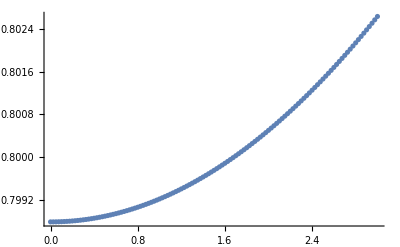

```mathematica
ListPlot[bands]
```

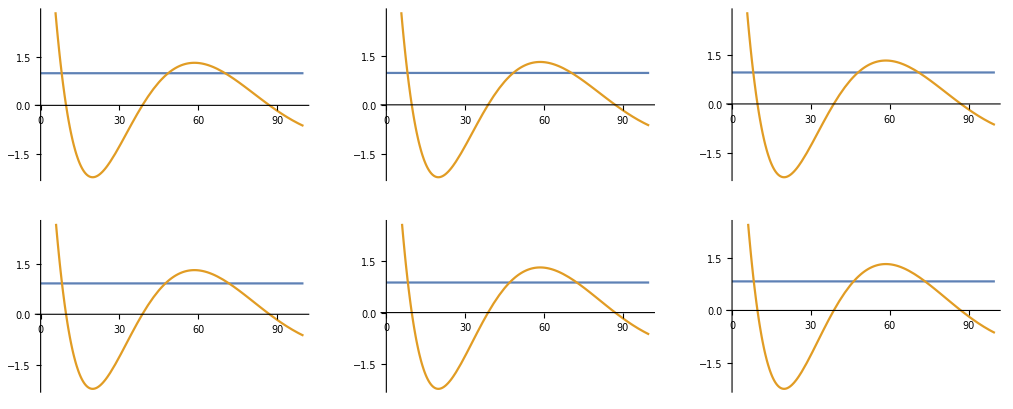

```mathematica
Table[Plot[{Cos[n/L a],(Cos[Sqrt[en]a]+V0/Sqrt[en] Sin[Sqrt[en]a])/π^2},{en,0,100}],{n,1,6}]//Partition[#,3]&//GraphicsGrid
```

```mathematica
(en/.FindRoot[Cos[2/L a]==Cos[Sqrt[en]a]+(2V0)/Sqrt[en] Sin[Sqrt[en]a],{en,2.9}]⟦1⟧)
```

9.67706

```mathematica
3.03/π^2
```

0.307003